```mathematica
ClearAll["Global`*"];
```

### Wprowadzenie wzoru na zdolność emisyjna ciała doskonale czarnego "ϵ[ν_,T_]" zależną od temperatury "T" ciała i częstotliwości "ν" emitowanego promieniowania elektromagnetycznego.

```mathematica
ϵ[ν_,T_]=(2×π×ν^2)/c^2×(h×ν)/(Exp[(h×ν)/(k×T)]-1);
```

### Obliczenie mocy "W" emitowanej z jednostki powierzchni ciała doskonale czarnego w całym zakresie częstotliwości.

```mathematica
W=Integrate[ϵ[ν,T],{ν,0,Infinity},Assumptions->Re[h/(k×T)]>0]
```

(2 k^4 π^5 T^4)/(15 c^2 h^3)

### Wyodrębnienie we wzorze na "W" czynnika stojącego przy T^4 (stałej Stefana - Boltzmanna) i nadaniu mu symbolu "σ".

```mathematica
σ=Coefficient[W,T^4]
```

(2 k^4 π^5)/(15 c^2 h^3)

### Obliczenie stałej Stefana - Boltzmanna.

```mathematica
σ/.{k->UnitConvert[Quantity["BoltzmannConstant"]],c->UnitConvert[Quantity["SpeedOfLight"]], h->UnitConvert[Quantity["PlanckConstant"]]}//N
```

5.67037×10^-8 kg/(s^3 K^4)

### Wprowadzenie wzoru na zdolność emisyjną ciała doskonale czarnego "ϵ[λ_,T_]" zależną od temperatury "T" ciała i długości "λ" emitowanego promieniowania elektromagnetycznego.

```mathematica
ϵ[λ_,T_]=c/λ^2×ϵ[ν,T]/.ν->c/λ
```

(2 c^2 h π)/((-1+ⅇ^((c h)/(k T λ))) λ^5)

### Obliczenie pochodnej "(∂ϵ[λ,T])/(∂λ)" z uwzględnieniem podstawienia x =(h c)/(k T λ)i nadanie jej nazwy "poch".

```mathematica
poch=D[ϵ[λ,T], λ]/.c->x×(k× T ×λ)/h//Together
```

(2 k^2 π T^2 x^2 (5-5 ⅇ^x+ⅇ^x x))/((-1+ⅇ^x)^2 h λ^4)

### Obliczenie wartości x niepeniającego warunek zerowania się pochodnej "poch" (warunek istnienia maksimum funkcji "ϵ[λ_,T_]") .

```mathematica
A=Solve[ⅇ^x x-5 ⅇ^x+5==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0},{x→5+ProductLog[-5/ⅇ^5]}}

```mathematica
x=x/.A[[2,1]]//N
```

4.96511

### Wprowadzenie wzoru na długość fali "λ_max" dla której funkcja "ϵ[λ_,T_]" posiada maksimum (matematyczny zapis prawa Viena).

```mathematica
λmax=(h×c)/(k×x)×1/T/.{k->UnitConvert[Quantity["BoltzmannConstant"]],c->UnitConvert[Quantity["SpeedOfLight"]], h->UnitConvert[Quantity["PlanckConstant"]]}
```

(0.00289777 m K)/T

```mathematica
k=UnitConvert[Quantity["BoltzmannConstant"×("Kelvins")/("Joules")]]//N
c=UnitConvert[Quantity["SpeedOfLight"×("Seconds")/("Meters")]]//N
h=UnitConvert[Quantity["PlanckConstant"×1/("Joules"×"Seconds")]]//N
```

1.38065×10^-23

2.99792×10^8

6.62607×10^-34

### Sporządzenie wykresu funkcji "ϵ[λ_, T_]" dla temperatury T = 2.7 K.

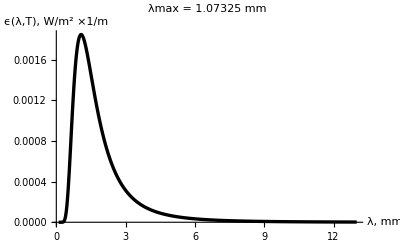

```mathematica
rys1=Plot[ϵ[λ×10^-3,2.7],{λ,1.0×10^-1,1.3×10^1},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{Black,Thickness[0.006]}},PlotRange->All,
PlotLabel->StyleForm[StringForm["                                    λmax  = ``    mm ",OutputForm[(h×c)/(k×x)×1/2.7×10^3]],FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"],
AxesLabel->{"λ, mm ","ϵ(λ,T), W/m^2 ×1/m"}]
```

### Sporządzenie wykresu funkcji "ϵ[λ_, T_]" dla temperatury T = 303 K.

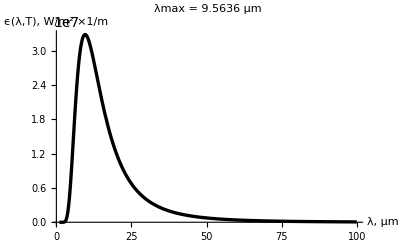

```mathematica
rys2=Plot[ϵ[λ×10^-6,303],{λ,1.0,1.0×10^2},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{Black,Thickness[0.006]}},PlotRange->All,
PlotLabel->StyleForm[StringForm["                                    λmax  = ``    μm ",OutputForm[(h×c)/(k×x)×1/303×10^6]],FontFamily->"Times",FontSlant->"Italic",
FontSize->12,FontWeight->"Bold"],
AxesLabel->{"λ, μm ","ϵ(λ,T), W/m^2 ×1/m"},
PlotLabel->StyleForm["   U",
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"]]
```

### Sporządzenie wykresu funkcji "ϵ[λ_, T_]" dla temperatury T = 6000 K.

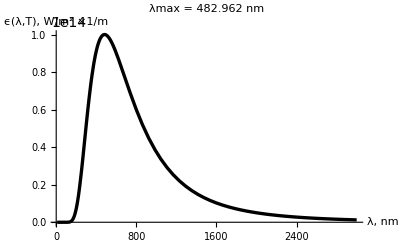

```mathematica
rys3=Plot[ϵ[λ×10^-9,6000],{λ,1.0×10^1,3.0×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{Black,Thickness[0.006]}},PlotRange->All,
PlotLabel->StyleForm[StringForm["                                    λmax  = ``    nm ",OutputForm[(h×c)/(k×x)×1/6000×10^9]],FontFamily->"Times",FontSlant->"Italic",
FontSize->12,FontWeight->"Bold"],
AxesLabel->{"λ, nm ","ϵ(λ,T), W/m^2 ×1/m"},
PlotLabel->StyleForm["   U",
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"]]
```